# 4QFT on SiDelft

### Modules

```mathematica
MatrixDist::usage="MatrixDist[matrix1, matrix2, plotglobalphase:False]. Calculate distance of 2 matrices by max_λ |(U-V)|, 
                    namely, maximum absolute eigenvalues of the matrix difference projected to the subspace of interest.";
MatrixDist[M1_,M2_,plotglobalphase_:False]:=Module[{globalphase,mindist,F,ϕ},
F[ϕ_?NumericQ]:=Max[Re@Sqrt[Abs@Eigenvalues[ConjugateTranspose[M1-Exp[ⅈ*ϕ]M2].(M1-Exp[ⅈ*ϕ]*M2)]]];
{mindist,globalphase}=NMinimize[{F[ϕ],0≤ϕ<2π},ϕ,PrecisionGoal->5,MaxIterations->1000];
If[plotglobalphase,Print@DiscretePlot[F[ϕ],{ϕ,0,2π,0.01},AxesLabel->{"ϕ","max_λ |Π_S(U-ⅇ^ⅈϕV)Π_S|"}]];
{mindist,ϕ/.globalphase}
]
HSDistance::usage="HSDistance[ansatz,θvars,unitary,nqubits]";
HSDistance[ansatz_,θvars_,unitary_,nqubits_]:=Module[{ψ1,ψ2,f},
{ψ1,ψ2}=CreateQuregs[2*nqubits,2];
ApplyCircuit[InitZeroState@ψ1,bellpairs[nqubits]];
ApplyCircuit[InitZeroState@ψ2,bellpairs[nqubits]];
ApplyCircuit[ψ1,{Subscript[U, Sequence@@Range[0,nqubits-1]][ConjugateTranspose@unitary]}];
ApplyCircuit[ψ1,ansatz/.θvars];
f=CalcFidelity[ψ1,ψ2];
DestroyQureg/@{ψ1,ψ2};
1-f
]
bellpairs::usage="create n-bell pairs";
bellpairs[n_,reverse_:False]:=With[{bp=Flatten[{Subscript[H, #1],Subscript[C, #1][Subscript[X, #2]]}&@@@Transpose@{Range[0,n-1],Range[n,2n-1]}]},If[reverse,Reverse@bp,bp]]
checkedConfψ[nqubit_,unitary_,ntrainstates_]:=Module[{conf,a},
While[True,
conf=DefaultConfig[nqubit,unitary,ntrainstates];
a=Gather[Times@@#&/@Values[varMeanInitStatesψ[conf]],Abs[#1-#2]<=10^-4&];
If[AllTrue[Length/@a,#==1&],
Break[]]
];
conf
]

checkedConfρ[dev_,unitary_,ntrainstates_,unitaryspace_:{}]:=Module[{conf,a},
While[True,
DestroyAllQuregs[];
conf=DefaultConfig[dev,unitary,ntrainstates,unitaryspace];
a=Gather[Times@@#&/@Values[varMeanInitStates[conf]],Abs[#1-#2]<=10^-4&];
If[AllTrue[Length/@a,#==1&],
Break[]]
];
conf
]

varMeanInitStatesψ::usage="varMeanInitStates[conf]. Calculate mean and variance of initial random states applied to the unitary.";
varMeanInitStatesψ[conf_]:=Module[{weights,ψwork,ψ,vm,g},
ψwork=CreateQureg[conf["nqubit"]];
ψ=CreateQureg[conf["nqubit"]];
vm=Association[
Table[
CloneQureg[ψ,conf["ψinit"][k]];
ApplyCircuit[ψ,conf["undocirc"][k]];
g=Calc2QubitCorr[conf["nqubit"],ψ,ψwork];
weights=PropertyValue[g,EdgeWeight];
k->{Mean[weights],Variance[weights]}
,{k,Keys@conf["ψinit"]}]];
DestroyQureg[ψwork];
DestroyQureg[ψ];
vm
]
```

### Definition of ansatze and sanity check

```mathematica
ansatz={Subscript[Rx, 0][Subscript[θ, 120]],Subscript[Ry, 3][Subscript[θ, 56]],Subscript[Ry, 0][Subscript[θ, 123]],Subscript[C, 2][Subscript[Ph, 3][Subscript[θ, 59]]],Subscript[Rx, 0][Subscript[θ, 124]],Subscript[SWAP, 1,2],Subscript[Ry, 1][Subscript[θ, 42]],Subscript[C, 0][Subscript[Ph, 1][Subscript[θ, 50]]],Subscript[Ry, 0][Subscript[θ, 7]],Subscript[C, 1][Subscript[Ph, 2][Subscript[θ, 33]]],Subscript[Rx, 0][Subscript[θ, 17]],Subscript[SWAP, 2,3],Subscript[Rx, 1][Subscript[θ, 9]],Subscript[C, 2][Subscript[Ph, 3][Subscript[θ, 11]]],Subscript[SWAP, 2,3],Subscript[Rx, 3][Subscript[θ, 15]],Subscript[Ry, 2][Subscript[θ, 68]],Subscript[Ry, 3][Subscript[θ, 16]],Subscript[Rx, 2][Subscript[θ, 69]],Subscript[SWAP, 1,2],Subscript[SWAP, 2,3],Subscript[C, 0][Subscript[Ph, 1][Subscript[θ, 97]]],Subscript[SWAP, 1,2],Subscript[C, 0][Subscript[Ph, 1][Subscript[θ, 103]]],Subscript[Ry, 0][Subscript[θ, 104]],Subscript[SWAP, 1,2],Subscript[SWAP, 2,3]};
θvars=<|Subscript[θ, 7]->3.1415553081326135,Subscript[θ, 9]->-3.1415902761443144,Subscript[θ, 11]->-5.497781449174974,Subscript[θ, 15]->3.141592396414565,Subscript[θ, 16]->3.141589972815106,Subscript[θ, 17]->-3.141586998968119,Subscript[θ, 33]->-1.5707929977286346,Subscript[θ, 42]->1.570798121323009,Subscript[θ, 50]->-0.7853987794252625,Subscript[θ, 56]->-1.5708008555616957,Subscript[θ, 59]->1.5707925829678986,Subscript[θ, 68]->1.570804921837841,Subscript[θ, 69]->-1.570796911567822,Subscript[θ, 97]->1.5707970860430527,Subscript[θ, 103]->0.3927006396217121,Subscript[θ, 104]->1.5707772216030695,Subscript[θ, 120]->-1.5707621567171606,Subscript[θ, 123]->0.7853977194886816,Subscript[θ, 124]->1.5707583339002782|>;
```

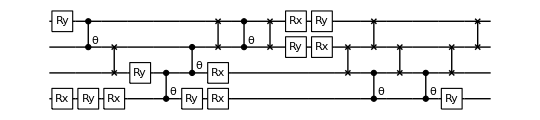

```mathematica
DrawCircuit[ansatz,4]
```

Distances given pristine qubits

```mathematica
unitary=CalcCircuitMatrix[DeleteCases[GetKnownCircuit["QFT",4],Subscript[SWAP, __]]];
```

```mathematica
MatrixDist[unitary,CalcCircuitMatrix[ansatz/.θvars]]
```

{0.0000172466,1.1781}

```mathematica
HSDistance[ansatz,θvars,unitary,4]
```

1.16543×10^-10

Use native gates, refine the search and check the new distance for sanity check

```mathematica
CustomGatesDefinitions
```

{SWAP_(p_,q_):>Sequence@@{Rx_p[π/2],C_p[Z_q],Rx_p[π/2],Rx_q[π/2],C_p[Z_q],Rx_p[π/2],Rx_q[π/2],C_p[Z_q],Rx_p[π/2]},PSW_(index1_,index2_)[θ_]:>U_(index1,index2)[{{1,0,0,0},{0,ⅇ^((ⅈ θ)/2) Cos[θ/2],-ⅈ ⅇ^((ⅈ θ)/2) Sin[θ/2],0},{0,-ⅈ ⅇ^((ⅈ θ)/2) Sin[θ/2],ⅇ^((ⅈ θ)/2) Cos[θ/2],0},{0,0,0,1}}]}

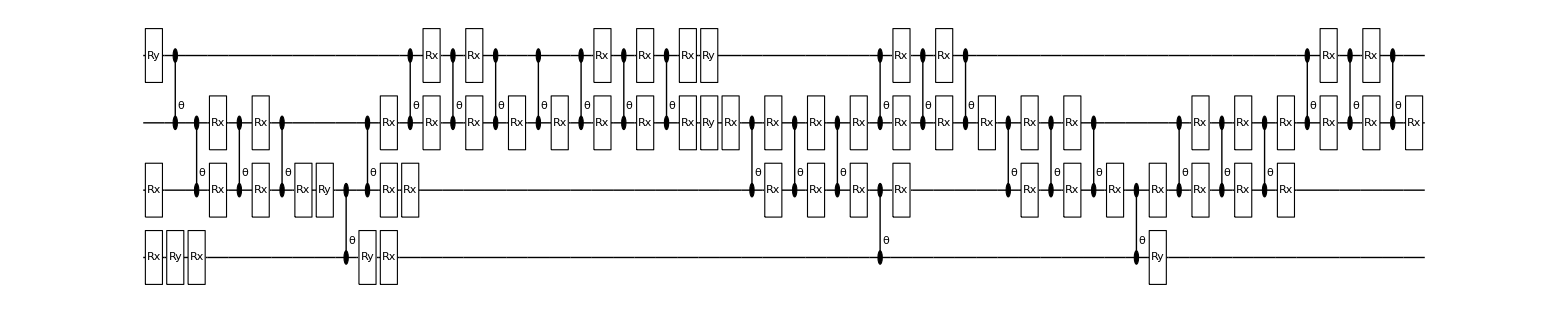

```mathematica
DrawCircuit[ansatz/.toSiGates,4]
```

```mathematica
HSDistance[ansatz/.CustomGatesDefinitions,θvars,unitary,4]
```

1.16544×10^-10

### Four qubits Silicon device

```mathematica
Options[SiliconDelft]={
qubitsNum->4,
T1->10^4,
T2-><|0-> 40.1,1-> 37.2,2-> 44.7,3-> 26.7|>,
QubitFreq-><|0-> 16.3*10^3,1-> 16.1*10^3,2-> 15.9*10^3,3-> 15.69*10^3|>,
RabiFreq-><|0->5,1->5,2->5,3->5|>,
OffResonantRabi->True,
StdPassiveNoise->True,
FidSingleXY-><|0-> 0.9996,1-> 0.9988,2-> 0.9991,3-> 0.9989|>,
EFSingleXY->{0,1},
FreqCZ-><|0-> 6.6,1-> 9.8,2-> 5.4|>,
FidCZ-><|0->0.9166807085341168,1->0.9805456134451412,2->0.9649648861853775|>,
EFCZ->{0,1},
ExchangeRotOn->{{0,0.07,0.042},{0.031,0,0.25},{0.02,0.03,0}},
ExchangeRotOff-><|0->0.03 ,1->0.02,2-> 0.028|>,
FidRead->0.99,
DurRead->10};
```

### Using noisy natural gradient

```mathematica
dev=SiliconDelft[];
conf=checkedConfρ[dev,unitary,10,{0,1,2,3}];
conf["ansatz"]=ansatz;
conf["θvars"]=θvars;
conf["grad"]="NGAN";
CircuitSynthesis[4,conf]
```

Compilation with predetermined ansatz using gradient methode NGAN

$Aborted